# Monkeypox Parameter Optimization

## Initializing Data

```mathematica
Import["/Users/wagner.palacio/Documents/Projeto/Repos/SystemModeling/Projects/Monkeypox/SEIQREpidemiologyModel.m"];
Import["https://raw.githubusercontent.com/antononcube/SystemModeling/master/Projects/Coronavirus-propagation-dynamics/WL/EpidemiologyModelModifications.m"];
Import["https://raw.githubusercontent.com/antononcube/SystemModeling/master/Projects/Coronavirus-propagation-dynamics/WL/EpidemiologyModelingVisualizationFunctions.m"];
Import["https://raw.githubusercontent.com/antononcube/SystemModeling/master/WL/SystemDynamicsInteractiveInterfacesFunctions.m"];
$PlotTheme = "Scientific";
```

Importing from GitHub:  EpidemiologyModels.m

```mathematica
cievsPEData := Import["https://raw.githubusercontent.com/palaciowagner/SystemModeling/master/Projects/Monkeypox/data/Pernambuco/Monkeypox%20-%20Pernambuco.csv", 
   "Dataset", "HeaderLines" -> 1];
owdPEData := Import["https://raw.githubusercontent.com/palaciowagner/SystemModeling/master/Projects/Monkeypox/data/OWD/latest_deprecated.csv", "Dataset", "HeaderLines" -> 1];
```

```mathematica
dateFormat = {"Day", "/", "Month", "/", "Year"};
PEdataMap = cievsPEData // Normal;
owdPEDataMap = Query[Select[StringContainsQ[ #Country, "Brazil"] && StringContainsQ[#Location, "Pernambuco"] && StringContainsQ[#Status, "confirmed"]&]] @ owdPEData;
```

```mathematica
pernambucoPopulation = QuantityMagnitude[9674793]; 
recifePopulation =  QuantityMagnitude[1661017]; 
maleInfected = 82.6/100;(*Cievs/PE. Dados atualizados em 10.11.2022, 15h.*)
estimatedInitialSusceptiblePopulation = ((recifePopulation/pernambucoPopulation)*maleInfected)*recifePopulation
```

235552.

```mathematica
groupedByDateOWD = GroupBy[Normal[owdPEDataMap], FromDateString[#"Date_confirmation", {"Year", "-", "Month", "-", "Day"}]&,Length] // Normal;
groupedCievs= Map[FromDateString[#Inicio, dateFormat]-> #"Confirmados" &,PEdataMap];
confirmadosJoined = Union[groupedByDateOWD, Take[groupedCievs, {15,-1}]] 
totalJoinedSmoothed = SmoothPeriod[Accumulate[TimeSeries[confirmadosJoined, TemporalRegularity->True]], 4, "Align"->Left];
(*SmoothPeriod[TimeSeries[Map[{FromDateString[#Inicio, dateFormat], #"Confirmados"} &,PEdataMap], TemporalRegularity -> True], 4, "Align"->Left]*)
(*totalConfirmadosOWDPE=Smooth[Accumulate[TimeSeries[groupedByDateOWD, TemporalRegularity->True]]];*)
totalConfirmadosPE = 
    SmoothPeriod[Accumulate[TimeSeries[Map[{FromDateString[#Inicio, dateFormat], #"Confirmados"} &,PEdataMap], TemporalRegularity -> True]], 4, "Align"->Left];
```

{Thu 21 Jul 2022→2,Fri 29 Jul 2022→4,Fri 5 Aug 2022→3,Sat 6 Aug 2022→3,Fri 12 Aug 2022→2,Tue 16 Aug 2022→1,Thu 18 Aug 2022→3,Wed 24 Aug 2022→4,Fri 26 Aug 2022→1,Mon 29 Aug 2022→1,Wed 31 Aug 2022→3,Thu 1 Sep 2022→14,Sun 4 Sep 2022→6,Tue 6 Sep 2022→1,Thu 8 Sep 2022→8,Fri 9 Sep 2022→4,Tue 13 Sep 2022→7,Wed 14 Sep 2022→23,Thu 15 Sep 2022→5,Fri 16 Sep 2022→12,Sat 17 Sep 2022→4,Tue 20 Sep 2022→7,Fri 23 Sep 2022→8,Tue 27 Sep 2022→2,Fri 30 Sep 2022→16,Tue 4 Oct 2022→10,Fri 7 Oct 2022→10,Tue 11 Oct 2022→0,Fri 14 Oct 2022→0,Tue 18 Oct 2022→1,Fri 21 Oct 2022→0,Tue 25 Oct 2022→3,Fri 28 Oct 2022→10,Tue 1 Nov 2022→8,Fri 4 Nov 2022→24,Tue 8 Nov 2022→3}

```mathematica
initialInfected =  Normal[totalJoinedSmoothed][[1]][[2]]
realIPData = <|"Infected"-> Ceiling[totalJoinedSmoothed["Values"]] // Normal|>
lsFocusParams = {β, α1, α2};
```

2

<|Infected→{2,6,6,11,12,14,17,18,23,24,34,48,58,84,105,122,127,136,154,164,164,164,165,167,173,186,210}|>

## Literature Data

Alguns dados que tirei de  artigos sobre a dinâmica da Monkeypox que serão uteis para as formulas

#### Periodo de Incubação

```mathematica
incubation = Range[5, 21];
incubationPeriod = Mean[incubation];
incubationPeriod
```

13

#### Período de Infecção [1]

```mathematica
prodomalPhase = Range[0, 3];
rashPhase = Range[7, 21];
infectiousPeriod = Mean[Map[Median] @ {prodomalPhase, rashPhase}]
maxInfectiousPeriod = Max[prodomalPhase, rashPhase]
medianInfectiousPeriod = Flatten[ {prodomalPhase,rashPhase}]
```

31/4

21

{0,1,2,3,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21}

#### Taxa de Recuperação (γ)

De acordo com [2], γ ==1/λ, sendo λ a média do período de infecção total.

## Otimização de parâmetros (β, α1, α2) dinâmico

### Taxa de Propagação ρT

```mathematica
(* Propagation Rate *)
ρt[t_, ζ_] := (NIP[t-5] +NIP[t-4]+ NIP[t-3])/(NIP[t-5-ζ] + NIP[t-4-ζ]+NIP[t-3-ζ])
(* Moving Average of Propagation Rate *)
(*ρT[T_,t_, ζ_]=Sum[ρt[t+i, ζ],{i,-(T-1)/2,(T-1)/2}]*1/T*)
equation := ρT'[t]== Sum[ρt[t+i, ζ],{i,-(T-1)/2,(T-1)/2}]*1/T
```

```mathematica
nonAccumulatedInfected = SmoothPeriod[TimeSeries[confirmadosJoined, TemporalRegularity->True], 4, "Align"->Left]
infectedAsMap = Normal@nonAccumulatedInfected
points ={ToModelTime[First@First@infectedAsMap, #1], #2}& @@@ Normal[nonAccumulatedInfected] //Echo[#, "", Multicolumn]&
infectedValues = Association@Map[First@# -> Last@#&,points]
chunk = 7;
```

TimeSeries[…]

{{Thu 21 Jul 2022 00:00:00GMT-3,2},{Mon 25 Jul 2022 00:00:00GMT-3,4},{Fri 29 Jul 2022 00:00:00GMT-3,4},{Tue 2 Aug 2022 00:00:00GMT-3,3},{Sat 6 Aug 2022 00:00:00GMT-3,3},{Wed 10 Aug 2022 00:00:00GMT-3,2},{Sun 14 Aug 2022 00:00:00GMT-3,2},{Thu 18 Aug 2022 00:00:00GMT-3,3},{Mon 22 Aug 2022 00:00:00GMT-3,3},{Fri 26 Aug 2022 00:00:00GMT-3,1},{Tue 30 Aug 2022 00:00:00GMT-3,9},{Sat 3 Sep 2022 00:00:00GMT-3,4},{Wed 7 Sep 2022 00:00:00GMT-3,6},{Sun 11 Sep 2022 00:00:00GMT-3,12},{Thu 15 Sep 2022 00:00:00GMT-3,7},{Mon 19 Sep 2022 00:00:00GMT-3,8},{Fri 23 Sep 2022 00:00:00GMT-3,5},{Tue 27 Sep 2022 00:00:00GMT-3,9},{Sat 1 Oct 2022 00:00:00GMT-3,10},{Wed 5 Oct 2022 00:00:00GMT-3,10},{Sun 9 Oct 2022 00:00:00GMT-3,0},{Thu 13 Oct 2022 00:00:00GMT-3,0},{Mon 17 Oct 2022 00:00:00GMT-3,1},{Fri 21 Oct 2022 00:00:00GMT-3,2},{Tue 25 Oct 2022 00:00:00GMT-3,7},{Sat 29 Oct 2022 00:00:00GMT-3,8},{Wed 2 Nov 2022 00:00:00GMT-3,24}}

{0,2} | {20,2} | {40,9} | {60,8} | {80,0} | {100,8}
{4,4} | {24,2} | {44,4} | {64,5} | {84,0} | {104,24}
{8,4} | {28,3} | {48,6} | {68,9} | {88,1} | 
{12,3} | {32,3} | {52,12} | {72,10} | {92,2} | 
{16,3} | {36,1} | {56,7} | {76,10} | {96,7} |

{{0,2},{4,4},{8,4},{12,3},{16,3},{20,2},{24,2},{28,3},{32,3},{36,1},{40,9},{44,4},{48,6},{52,12},{56,7},{60,8},{64,5},{68,9},{72,10},{76,10},{80,0},{84,0},{88,1},{92,2},{96,7},{100,8},{104,24}}

<|0→2,4→4,8→4,12→3,16→3,20→2,24→2,28→3,32→3,36→1,40→9,44→4,48→6,52→12,56→7,60→8,64→5,68→9,72→10,76→10,80→0,84→0,88→1,92→2,96→7,100→8,104→24|>

```mathematica
ClearAll[NIP];
ClearAll[ρT];
ClearAll[eq2];
ClearAll[func];
ClearAll[getFrom];
```

```mathematica
getFrom[list_Association,t_Integer, T_Integer] :=  Module[{vals},
vals = Values@list;
vals[[#]][Floor[(t/T)+1]]&
];
(*func := eq2'[t] == getFrom[infectedValues, t, T];*)
```

```mathematica
initial = <|T->chunk, ζ->13|> 
rateRules ={
NIP'[t] == getFrom[infectedValues, t, T],
(*NIP[t /; Floor[N[t/T]]==0]== Function[Indexed[list,#]][(t/T)+1],
NIP[t /; Quotient[t,T]!=0]== Function[Indexed[list,#]][(t - Quotient[t,T])+1],*)
ρT[t /; t<=0] == 1,
NIP[t /; t<= 0] == First@infectedValues,
eq2[t /; t<=0] == First@infectedValues
}
```

<|T→7,ζ→13|>

Solve::naqs: getFrom[<|0→2,4→4,8→4,12→3,16→3,20→2,24→2,28→3,32→3,36→1,40→9,44→4,48→6,52→12,56→7,60→8,64→5,68→9,72→10,76→10,80→0,84→0,88→1,92→2,96→7,100→8,104→24|>,t,T] is not a quantified system of equations and inequalities.

{NIP'[t]==Solve[getFrom[<|0→2,4→4,8→4,12→3,16→3,20→2,24→2,28→3,32→3,36→1,40→9,44→4,48→6,52→12,56→7,60→8,64→5,68→9,72→10,76→10,80→0,84→0,88→1,92→2,96→7,100→8,104→24|>,t,T]],ρT[t/;t≤0]==1,NIP[t/;t≤0]==2,eq2[t/;t≤0]==2}

```mathematica
func
```

eq2'[t]==getFrom[<|0→2,4→4,8→4,12→3,16→3,20→2,24→2,28→3,32→3,36→1,40→9,44→4,48→6,52→12,56→7,60→8,64→5,68→9,72→10,76→10,80→0,84→0,88→1,92→2,96→7,100→8,104→24|>,t,T]

```mathematica
propagationEquation =  Flatten @{equation,rateRules} //.initial
```

{ρT'[t]==1/7 ((NIP[-8+t]+NIP[-7+t]+NIP[-6+t])/(NIP[-21+t]+NIP[-20+t]+NIP[-19+t])+(NIP[-7+t]+NIP[-6+t]+NIP[-5+t])/(NIP[-20+t]+NIP[-19+t]+NIP[-18+t])+(NIP[-6+t]+NIP[-5+t]+NIP[-4+t])/(NIP[-19+t]+NIP[-18+t]+NIP[-17+t])+(NIP[-5+t]+NIP[-4+t]+NIP[-3+t])/(NIP[-18+t]+NIP[-17+t]+NIP[-16+t])+(NIP[-4+t]+NIP[-3+t]+NIP[-2+t])/(NIP[-17+t]+NIP[-16+t]+NIP[-15+t])+(NIP[-3+t]+NIP[-2+t]+NIP[-1+t])/(NIP[-16+t]+NIP[-15+t]+NIP[-14+t])+(NIP[-2+t]+NIP[-1+t]+NIP[t])/(NIP[-15+t]+NIP[-14+t]+NIP[-13+t])),NIP'[t]==getFrom[<|0→2,4→4,8→4,12→3,16→3,20→2,24→2,28→3,32→3,36→1,40→9,44→4,48→6,52→12,56→7,60→8,64→5,68→9,72→10,76→10,80→0,84→0,88→1,92→2,96→7,100→8,104→24|>,t,7],ρT[t/;t≤0]==1,NIP[t/;t≤0]==2,eq2[t/;t≤0]==2}

```mathematica
ResourceFunction["GridTableForm"][List /@ propagationEquation]
```

# | 1
1 | ρT'[t]==1/7 ((NIP[-8+t]+NIP[-7+t]+NIP[-6+t])/(NIP[-21+t]+NIP[-20+t]+NIP[-19+t])+(NIP[-7+t]+NIP[-6+t]+NIP[-5+t])/(NIP[-20+t]+NIP[-19+t]+NIP[-18+t])+(NIP[-6+t]+NIP[-5+t]+NIP[-4+t])/(NIP[-19+t]+NIP[-18+t]+NIP[-17+t])+(NIP[-5+t]+NIP[-4+t]+NIP[-3+t])/(NIP[-18+t]+NIP[-17+t]+NIP[-16+t])+(NIP[-4+t]+NIP[-3+t]+NIP[-2+t])/(NIP[-17+t]+NIP[-16+t]+NIP[-15+t])+(NIP[-3+t]+NIP[-2+t]+NIP[-1+t])/(NIP[-16+t]+NIP[-15+t]+NIP[-14+t])+(NIP[-2+t]+NIP[-1+t]+NIP[t])/(NIP[-15+t]+NIP[-14+t]+NIP[-13+t]))
2 | NIP'[t]==getFrom[<|0→2,4→4,8→4,12→3,16→3,20→2,24→2,28→3,32→3,36→1,40→9,44→4,48→6,52→12,56→7,60→8,64→5,68→9,72→10,76→10,80→0,84→0,88→1,92→2,96→7,100→8,104→24|>,t,7]
3 | ρT[t/;t≤0]==1
4 | NIP[t/;t≤0]==2
5 | eq2[t/;t≤0]==2

```mathematica
propagationEquation
```

{ρT'[t]==1/7 ((NIP[-8+t]+NIP[-7+t]+NIP[-6+t])/(NIP[-21+t]+NIP[-20+t]+NIP[-19+t])+(NIP[-7+t]+NIP[-6+t]+NIP[-5+t])/(NIP[-20+t]+NIP[-19+t]+NIP[-18+t])+(NIP[-6+t]+NIP[-5+t]+NIP[-4+t])/(NIP[-19+t]+NIP[-18+t]+NIP[-17+t])+(NIP[-5+t]+NIP[-4+t]+NIP[-3+t])/(NIP[-18+t]+NIP[-17+t]+NIP[-16+t])+(NIP[-4+t]+NIP[-3+t]+NIP[-2+t])/(NIP[-17+t]+NIP[-16+t]+NIP[-15+t])+(NIP[-3+t]+NIP[-2+t]+NIP[-1+t])/(NIP[-16+t]+NIP[-15+t]+NIP[-14+t])+(NIP[-2+t]+NIP[-1+t]+NIP[t])/(NIP[-15+t]+NIP[-14+t]+NIP[-13+t])),NIP'[t]==getFrom[<|0→2,4→4,8→4,12→3,16→3,20→2,24→2,28→3,32→3,36→1,40→9,44→4,48→6,52→12,56→7,60→8,64→5,68→9,72→10,76→10,80→0,84→0,88→1,92→2,96→7,100→8,104→24|>,t,7],ρT[t/;t≤0]==1,NIP[t/;t≤0]==2,eq2[t/;t≤0]==2}

```mathematica
(*Clear[ρT];
Clear[NIP];*)
propagationSolution =  Solve[propagationEquation,ρT,{t}]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[{ρT'[t]==1/7 ((NIP[-8+t]+NIP[-7+t]+NIP[-6+t])/(NIP[-21+t]+NIP[-20+t]+NIP[-19+t])+(NIP[-7+t]+NIP[-6+t]+NIP[-5+t])/(NIP[-20+t]+NIP[-19+t]+NIP[-18+t])+(NIP[-6+t]+NIP[-5+t]+NIP[-4+t])/(NIP[-19+t]+NIP[-18+t]+NIP[-17+t])+(NIP[-5+t]+NIP[-4+t]+NIP[-3+t])/(NIP[-18+t]+NIP[-17+t]+NIP[-16+t])+(NIP[-4+t]+NIP[-3+t]+NIP[-2+t])/(NIP[-17+t]+NIP[-16+t]+NIP[-15+t])+(NIP[-3+t]+NIP[-2+t]+NIP[-1+t])/(NIP[-16+t]+NIP[-15+t]+NIP[-14+t])+(NIP[-2+t]+NIP[-1+t]+NIP[t])/(NIP[-15+t]+NIP[-14+t]+NIP[-13+t])),NIP'[t]==getFrom[<|0→2,4→4,8→4,12→3,16→3,20→2,24→2,28→3,32→3,36→1,40→9,44→4,48→6,52→12,56→7,60→8,64→5,68→9,72→10,76→10,80→0,84→0,88→1,92→2,96→7,100→8,104→24|>,t,7],ρT[t/;t≤0]==1,NIP[t/;t≤0]==2,eq2[t/;t≤0]==2},ρT,{t}]

```mathematica
params = propagationSolution[[1]]["Parameters"] //. <|list->infectedValues|>;
f=propagationSolution[[1]][Sequence@@params];
ts = Range@@ {0,1,1};
Transpose[{ts, f[ts]}];
```

Transpose::nmtx: The first two levels of {{0,1},(ρT→ParametricFunction[1,«5»,{NDSolve`base$76750,NDSolve`NDSolveParametricFunction[0,{ParametricNDSolve,Internal`Bag[<2>],None,ParametricNDSolve},{{{«9»},{«9»}},{0,{«3»},{«2»},{«3»}},None,{{«7»},{},None,{}}},{ρT},{{Equal[«2»],Equal[«2»],Equal[«2»],Equal[«2»],Equal[«2»],Equal[«2»]},{},{},{},{}},{{0,«3»}},{Automatic,«9»,«17»},{Automatic,Automatic,MachinePrecision,Automatic,Automatic,Automatic,Automatic,None,None,Automatic,«17»},{Cache→True,CacheTableLength→19,CacheTableWidth→7,CacheKeyMaxBytes→1000000,CacheResultMaxBytes→1000000,KeyComparison→None,ResultComparison→LessEqual},{},«1»]}])[…s][«1»]} cannot be transposed.

```mathematica
propagationSolution
```

{ρT→ParametricFunction[<>]}

```mathematica
{"Cache","CacheKeyMaxBytes","CacheResultMaxBytes","CacheTableLength","CacheTableWidth","KeyComparison","ResultComparison",NIP,ρT}/.%686
```

{Cache,CacheKeyMaxBytes,CacheResultMaxBytes,CacheTableLength,CacheTableWidth,KeyComparison,ResultComparison,ParametricFunction[<>],ParametricFunction[<>]}

```mathematica
results1 =Map[ParametricFunctionValues[#,None, {0,27,1}]&, propagationSolution]
```

{ParametricFunctionValues[ρT→ParametricFunction[<>],None,{0,27,1}]}

### Definição do Modelo

```mathematica
ClearAll[modelSEIQRDynamicBeta];
modelSEIQRDynamicBeta = With[{contactRate=ToExpression["Global`"<>"β"]},
model = SEIQRModel[t, "InitialConditions" -> True, "RateRules" -> True, 
   "TotalPopulationRepresentation" -> "Constant"];
(*lsRepRules={
contactRate -> contactRate[t]
};
(*model["Rates"] = KeyDrop[model["Rates"], {contactRate}];*)
model["Rates"]=KeyMap[#/. lsRepRules&,model["Rates"]];
model["Equations"]=Map[#/. lsRepRules&,model["Equations"]];
model["RateRules"]=Association[Normal[model["RateRules"]]/. lsRepRules];
model["RateRules"]=KeyDrop[model["RateRules"],{contactRate[t]}];*)
(*AppendTo[model["Stocks"],NIP[t]->"Newly Infected Population"];
AppendTo[model["Stocks"],PR[t]->"Propagation Rate"];*)model["InitialConditions"]=ReplacePart[model["InitialConditions"],3-> IP[t /; t<=0]==initialInfected];
(*AppendTo[modelSEIQRDynamicBeta["InitialConditions"], NIP[t/; IP[-1+t]+IP[t]===0]==1];*)
(*AppendTo[model["InitialConditions"], NIP[t /; t<=0]==1];
AppendTo[model["InitialConditions"], PR[t /; t<=0]==0];
AppendTo[model["Equations"], NIP'[t]==IP[t]-IP[t-1]];
AppendTo[model["Equations"], PR'[t]==ρT[7,t, ζ] ];*)
(*AppendTo[model["Equations"], ρ'[T]==((ρ[t-6] + ρ[t-5] +ρ[t-4] + ρ[t-3]+ ρ[t-2]+ρ[t])/T ];*)

(*AppendTo[model["InitialConditions"],  β[t /; t<=0]==0.001];*)
model];
```

```mathematica
modelSEIQRDynamicBeta = SetRateRules[modelSEIQRDynamicBeta, 
<|NP[0] -> Round[estimatedInitialSusceptiblePopulation/100],
λ-> infectiousPeriod,
ζ->incubationPeriod|>
];
modelSEIQRDynamicBeta = SetInitialConditions[modelSEIQRDynamicBeta,
   <|
SP[0] ->  Round[estimatedInitialSusceptiblePopulation/100],
EP[0] -> 2,
QP[0] -> 8
    |>];
```

```mathematica
lsActualEquationsDynamicBeta = Join[modelSEIQRDynamicBeta["Equations"]//.KeyDrop[modelSEIQRDynamicBeta["RateRules"], lsFocusParams],modelSEIQRDynamicBeta["InitialConditions"]]
ModelGridTableForm[modelSEIQRDynamicBeta]
```

```mathematica
asolDynamicBeta = Association @ Flatten@ParametricNDSolve[lsActualEquationsDynamicBeta,{SP,EP,IP,QP, RP},{t,0,100},lsFocusParams, Method->Automatic,MaxStepSize->1, StartingStepSize->1]
```

```mathematica
ResourceFunction["GridTableForm"][List /@ lsActualEquationsDynamicBeta]
```

```mathematica
asolDynamicBeta[[4]][0.517,0.729, 0.692]
```

```mathematica
allValues =Map[ParametricFunctionValues[#,<|β->0.517,α1->0.729,α2->0.692|>, {0,100,1}]&, asolDynamicBeta]
```

```mathematica
(*positions = Flatten@Values@ PositionIndex @ Keys[ modelSEIQRDynamicBeta["Stocks"]];
First@positions*)
```

```mathematica
(*({#[20]})& /@ asolDynamicBeta *)
```

```mathematica
opts={PlotRange->All,PlotLegends->None,PlotTheme->"Detailed",PerformanceGoal->"Speed",ImageSize->800};
Manipulate[
DynamicModule[{lsPopulationPlots2},
lsPopulationPlots2=
Quiet[ParametricSolutionsPlots[
modelSEIQRDynamicBeta["Stocks"],
KeyTake[asolDynamicBeta,GetPopulationSymbols[modelSEIQRDynamicBeta, __ ~~ "Population"]],{contactRate, alpha1, alpha2},nWeeks,"Together"->popTogetherQ,opts]];
  Show[lsPopulationPlots2[[3]],ListPlot[PadRealData[realIPData,Round[incubationPeriod+padOffset],Round[infectionPeriod+padOffset]],PlotStyle->{Blue,Black,Red}]]
  (*Multicolumn[plots, nPlotColumns, Dividers -> All, 
   FrameStyle -> GrayLevel[0.8]]*)
],
{{population,estimatedInitialSusceptiblePopulation/100,"Population"},100,estimatedInitialSusceptiblePopulation,50,Appearance->{"Open"}},
{{padOffset,0,"real data padding offset"},-100,100,1,Appearance->{"Open"}},
{{contactRate, 0.540, StringJoin["Contact rate of the infected population (β)", ToString[DisplayForm[InterpretationBox[SuperscriptBox["10", "-4"], var]]]]}, 0.001, 1, 0.001, 
  Appearance -> {"Open"}},
 {{incubationPeriod, 13, "Incubation period (ζ) in days "}, 5, 21, 1, 
  Appearance -> {"Open"}},
 {{alpha1, 0.718, "Alpha 1(α1)"}, 0, 1, 0.001, 
  Appearance -> {"Open"}},
 {{alpha2, 0.693, "Alpha 2(α2)"}, 0, 1, 0.001, 
  Appearance -> {"Open"}},
 {{infectionPeriod,7, "Infection period (λ) in days "}, 0, 21, 1, 
  Appearance -> {"Open"}},
 {{nWeeks,28, "Epidemiological Week (t)"}, 1, 52, 1, Appearance -> {"Open"}},
 {{nPlotColumns, 1, "Number of plot columns"}, Range[3]}, 
{{popTogetherQ, False, "Plot populations together"}, {False, True}},
ControlPlacement->Left,ContinuousAction->False]
```

Show::gcomb: Could not combine the graphics objects in Show[{0.54,0.718,0.693},].

ListPlot::lpn: SEIQREpidemiologyModel`PadRealData[realIPData,12.,6.] is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[{0.517,0.729,0.692},ListPlot[SEIQREpidemiologyModel`PadRealData[realIPData,12,6],PlotStyle→{color,color,color}]].

Show::gcomb: Could not combine the graphics objects in Show[{0.517,0.729,0.692},].

ListPlot::lpn: SEIQREpidemiologyModel`PadRealData[realIPData,13.,7.] is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[{0.54,0.718,0.693},ListPlot[SEIQREpidemiologyModel`PadRealData[realIPData,13,7],PlotStyle→{color,color,color}]].

Show::gcomb: Could not combine the graphics objects in Show[{0.54,0.718,0.693},].

## Simulações

```mathematica
totalNewlyInfectedOptimizedDynamic = SmoothPeriod[Accumulate[TimeSeries[confirmadosJoined, TemporalRegularity->True]],7, "Align"-> Left] // Normal
```

```mathematica
(*totalSusceptibleOptimized = SmoothPeriod[Accumulate[TimeSeries[expostosJoined, TemporalRegularity->True]],maxInfectiousPeriod] // Normal*)
firstDateInfectedDynamic = First @ First@Normal[totalNewlyInfectedOptimizedDynamic];
lastDateInfectedDynamic = First @  Last@ Normal[totalNewlyInfectedOptimizedDynamic];
fitInfectedDataDynamic={ToModelTime[firstDateInfectedDynamic, #1], #2}& @@@ Normal[totalNewlyInfectedOptimizedDynamic] //Echo[#, "", Multicolumn]&;
```

```mathematica
newlyInfectedSol =  Association@Flatten@Quiet[ParametricNDSolve[lsActualEquationsDynamicBeta,{SP,EP,IP,QP, RP},{t,0,100},lsFocusParams,MaxStepSize->1, StartingStepSize->1]];
{infectedSolDynamic, betaSolDynamic}= {IP[β,α1,α2], PR[β,α1,α2]} /.newlyInfectedSol;
currentDynamic = Take[totalNewlyInfectedOptimizedDynamic,15]
```

```mathematica
all = {ToModelTime[First@First@Normal[currentDynamic], #1], #2}& @@@ Normal[currentDynamic]
s01 = Take[all,4]
s02=Take[all,{4,7}]
s03=Take[all,{7,10}]
s04=Take[all,{10,13}]
s05=Take[all,-3]
```

### Simulação 1

```mathematica
AbsoluteTiming[fitInfectedDynamic=NonlinearModelFit[s01,{infectedSolDynamic[t], {β >0 && α1 >0 &&  α2 >0}},{{β,0.517}, {α1,0.729},{α2,0.692}},t, EvaluationMonitor:> Print["β=", β,"  .α1=",α1,"   .α2=",α2],Method-> {NMinimize, Method->{"NelderMead", "PostProcess"-> {"FindMinimum"}}}]]
```

```mathematica
Quiet @ fitInfectedDynamic["ParameterTable"]
Quiet @ fitInfectedDynamic["BestFitParameters"]
Quiet @fitInfectedDynamic["RSquared"]
Quiet @fitInfectedDynamic["AdjustedRSquared"]
Quiet @FitWithDataPlot[fitInfectedDynamic,{First@First@Normal[currentDynamic],First@Last@Normal[currentDynamic]} ]
```

### Simulação 2

```mathematica
resultsS01 =Map[ParametricFunctionValues[#,<|β->0.224,α1->1.00,α2->0|>, {0,21,1}]&, asolDynamicBeta];
s01AsMap = Map[Last[Last[Last[#]]]&,Normal@resultsS01]
```

```mathematica
Total[Take[s01AsMap,5]]
```

```mathematica
AbsoluteTiming[fitInfectedDynamic02=NonlinearModelFit[s02,{infectedSolDynamic[t], {β >0 && α1 >0 &&  α2 >0}},{{β,0.224}, {α1,1.},{α2,0.001}},t, EvaluationMonitor:> Print["β=", β,"  .α1=",α1,"   .α2=",α2],Method-> {NMinimize, Method->{"NelderMead", "PostProcess"-> {"FindMinimum"}}}]]
```

```mathematica
Quiet @ fitInfectedDynamic02["ParameterTable"]
Quiet @ fitInfectedDynamic02["BestFitParameters"]
Quiet @fitInfectedDynamic02["RSquared"]
Quiet @fitInfectedDynamic02["AdjustedRSquared"]
Quiet @FitWithDataPlot[fitInfectedDynamic02,{First@First@Normal[currentDynamic],First@Last@Normal[currentDynamic]} ]
```

```mathematica
Association@Quiet @ fitInfectedDynamic02["BestFitParameters"]
```

### Simulação 3

```mathematica
AbsoluteTiming[fitInfectedDynamic03=NonlinearModelFit[s03,{infectedSolDynamic[t], {0<β && 0<α1<=1 && 0< α2<=1}},{{β,0.217}, {α1,0.803},{α2,0.0170}},t, AccuracyGoal-> 3, WorkingPrecision-> 3,  PrecisionGoal -> 3, EvaluationMonitor:> Print["β=", β,"  .α1=",α1,"   .α2=",α2],Method-> {NMinimize, Method->{"NelderMead", "PostProcess"-> {"FindMinimum"}}}]]
```

```mathematica
Quiet @ fitInfectedDynamic03["ParameterTable"]
Quiet @ fitInfectedDynamic03["BestFitParameters"]
Quiet @fitInfectedDynamic03["RSquared"]
Quiet @fitInfectedDynamic03["AdjustedRSquared"]
Quiet @FitWithDataPlot[fitInfectedDynamic03,{First@First@Normal[currentDynamic],First@Last@Normal[currentDynamic]} ]
```

### Simulação 4

```mathematica
AbsoluteTiming[fitInfectedDynamic04=NonlinearModelFit[s04,{infectedSolDynamic[t], {0<β && 0<α1<=1 && 0< α2<=1}},{{β,0.356}, {α1,0.999},{α2,0.686}},t, AccuracyGoal-> 3, WorkingPrecision-> 3,  PrecisionGoal -> 3, EvaluationMonitor:> Print["β=", β,"  .α1=",α1,"   .α2=",α2],Method-> {NMinimize, Method->{"NelderMead", "PostProcess"-> {"FindMinimum"}}}]]
```

```mathematica
Quiet @ fitInfectedDynamic04["ParameterTable"]
Quiet @ fitInfectedDynamic04["BestFitParameters"]
Quiet @fitInfectedDynamic04["RSquared"]
Quiet @fitInfectedDynamic04["AdjustedRSquared"]
Quiet @FitWithDataPlot[fitInfectedDynamic04,{First@First@Normal[currentDynamic],First@Last@Normal[currentDynamic]} ]
```

### Simulação 5

```mathematica
AbsoluteTiming[fitInfectedDynamic05=NonlinearModelFit[s05,{infectedSolDynamic[t], {0<β && 0<α1<=1 && 0< α2<=1}},{{β,0.354}, {α1,0.377},{α2,0.216}},t, AccuracyGoal-> 3, WorkingPrecision-> 3,  PrecisionGoal -> 3, EvaluationMonitor:> Print["β=", β,"  .α1=",α1,"   .α2=",α2],Method-> {NMinimize, Method->{"NelderMead", "PostProcess"-> {"FindMinimum"}}}]]
```

```mathematica
Quiet @ fitInfectedDynamic05["ParameterTable"]
Quiet @ fitInfectedDynamic05["BestFitParameters"]
Quiet @fitInfectedDynamic05["RSquared"]
Quiet @fitInfectedDynamic05["AdjustedRSquared"]
Quiet @FitWithDataPlot[fitInfectedDynamic05,{First@First@Normal[currentDynamic],First@Last@Normal[currentDynamic]} ]
```

### Simulação Total

```mathematica
AbsoluteTiming[fitInfectedDynamicAll=NonlinearModelFit[all,{infectedSolDynamic[t], {β > 0 && 0<α1<=1  && 0<α2<=1}},{{β,0.517}, {α1,0.729},{α2,0.692}},t,Method-> {NMinimize, Method->{"NelderMead"}}]]
```

```mathematica
Quiet @ fitInfectedDynamicAll["ParameterTable"]
Quiet @ fitInfectedDynamicAll["BestFitParameters"]
Quiet @fitInfectedDynamicAll["RSquared"]
Quiet @fitInfectedDynamicAll["AdjustedRSquared"]
Quiet @FitWithDataPlot[fitInfectedDynamicAll,{First@First@Normal[currentDynamic],First@Last@Normal[currentDynamic]} ]
```

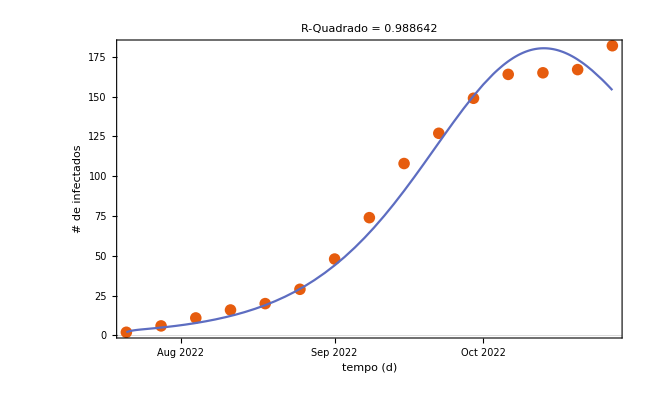

```mathematica
00001.260604874863131`3*10^-4
```

```mathematica
RealDigits[0.0001260604874863131`3.]
```

```mathematica
Chunk[list_,chunk_]:=Flatten[Partition[list,chunk][[#;;;;2]]]&/@{1,2}
```

```mathematica
fits ={fitInfectedDynamic, fitInfectedDynamic02, fitInfectedDynamic03, fitInfectedDynamic04, fitInfectedDynamic05}
```

```mathematica
JoinFittedDatePlot[fits_List,fitComplete_FittedModel,{dateMin_DateObject,dateMax_DateObject}]:=
Module[{plotAll,plotData,bands,cd, chunks},
cd=ColorData[108];
firstFit = First@fits;
lastFit = Last@fits;
plotAll={ToDataDate[dateMin,#1],#2}&@@@fitComplete["Data"];
plotData=Map[{ToDataDate[dateMin,#1],#2}&@@@#["Data"]&,fits];
bands[x_]=Quiet @ fitComplete["SinglePredictionBands",ConfidenceLevel->0.95]&/. t->x;
Show[DateListPlot[plotAll,Joined->True,PlotRange->All],
DateListPlot[plotData,Joined->False,PlotRange->All,PlotTheme->"Detailed"],
Plot[{fitComplete[ToModelTime[dateMin,FromAbsoluteTime@t]]&,
bands[ToModelTime[dateMin,FromAbsoluteTime@t]]},
{t,AbsoluteTime@dateMin,AbsoluteTime@dateMax},
PlotRange->All,
PlotStyle->{cd[2],None},
Filling->{2->{1}},
FillingStyle->{Opacity[0.5,Lighter@cd[2]]},
Exclusions->None],
PlotRange->All,
PlotRangePadding->{Automatic,{Scaled[0.03],Scaled[0.1]}},
FrameLabel->{"tempo (d)","# de infectados"},ImageSize->360,
PlotLabel->StringForm["Simulações com parâmetros ajustados"]]
//Labeled[#,Column[{LineLegend[{cd[1]},{"S00"}],PointLegend[{cd[2]},{"S01"}],PointLegend[{cd[3]},{"S02"}],PointLegend[{cd[4]},{"S03"}],PointLegend[{cd[5]},{"S04"}], PointLegend[{cd[6]},{"S05"}]},Left],Right]&]
```

```mathematica
JoinFittedDatePlot[fits,fitInfectedDynamicAll, {First@First@Normal[currentDynamic],First@Last@Normal[currentDynamic]}]
```

```mathematica
dateMin = First@First@Normal[currentDynamic];
dateMax = First@Last@Normal[currentDynamic];
bands[x_,t_]=Quiet @ Map[#["SinglePredictionBands",ConfidenceLevel->0.95]&/. t->x, fits]
```

## Modelo Final

```mathematica
(*lastFit = fitInfectedDynamic05 ;
lastParameters = Association@fitInfectedDynamic04["BestFitParameters"]*)
(*Normal@lastParameters[[2]]*)
(*lastFit["Data"]*)
lastParameters=<|β->0.332, α1->0.160, α2->0.053|>
resultsLastSimulation =Map[ParametricFunctionValues[#,<|β->0.332, α1->0.160, α2->0.053|>, {84,98,1}]&, asolDynamicBeta]
resultsLastSimulationMap = Map[Last[Last[Last[#]]]&,Normal@resultsLastSimulation]
```

```mathematica
modelSEIQRFinal = SetRateRules[modelSEIQRDynamicBeta, <|
NP[0] -> Total[resultsLastSimulationMap],  
β->Normal@lastParameters[[1]],
α1-> Normal@lastParameters[[2]],
α2->Normal@lastParameters[[3]]|>];
modelSEIQRFinal["InitialConditions"] = ReplacePart[modelSEIQRFinal["InitialConditions"], 3->IP[0]== resultsLastSimulationMap[[3]]]
modelSEIQRFinal = SetInitialConditions[modelSEIQRFinal,
   <|
SP[0] -> resultsLastSimulationMap[[1]],
EP[0] -> resultsLastSimulationMap[[2]],
IP[t ;/ t<=0] -> resultsLastSimulationMap[[3]],
QP[0] -> resultsLastSimulationMap[[4]],
RP[0] -> resultsLastSimulationMap[[5]]
    |>]; 

lsActualEquationsFinal = Join[modelSEIQRFinal["Equations"] //. KeyDrop[modelSEIQRFinal["RateRules"], {}], modelSEIQRFinal["InitialConditions"]]
modelSEIQRFinal["InitialConditions"]
ModelGridTableForm[modelSEIQRFinal]
ResourceFunction["GridTableForm"][List /@ lsActualEquationsFinal]
aSolFinal = NDSolve[lsActualEquationsFinal,{SP,EP,IP,QP, RP},{t,0,60}]
```

```mathematica
aSolForPeaks = Association@Flatten@ParametricNDSolve[lsActualEquationsFinal,{SP,EP,IP,QP, RP},{t,0,60},{β,α1,α2}]
```

```mathematica
allValues =Map[ParametricFunctionValues[#,lastParameters, {0,60,1}]&, aSolForPeaks];
peaks = Map[FindPeaks[Last/@#]&,allValues]
```

```mathematica
Clear[PadRealData];
PadRealData[aData:Association[(_String->_?VectorQ)..],incubationPeriod_?IntegerQ,infectiousPeriod_?IntegerQ]:=Block[{},Join[ConstantArray[0,incubationPeriod+infectiousPeriod],#]&/@aData];
```

```mathematica
optsFinal={PlotRange->All,PlotLegends->None,PlotTheme->"Detailed",PerformanceGoal->"Speed",ImageSize->800};
DynamicModule[{beta=Normal@lastParameters[[1]],alpha1=Normal@lastParameters[[2]],alpha2=Normal@lastParameters[[3]],nWeeks=60},
DynamicModule[{modelSEIQR=modelSEIQRFinal,lsFinal},
lsFinal = ParametricSolutionsPlots[modelSEIQR["Stocks"],#,None,nWeeks,"Together"->True,optsFinal]&/@GroupBy[Normal@aSolFinal,#[[1,1]]&,Association];
(*Show[List@Plot[Map[Identity[#]&,Values[aSolFinal]],{t,0,100}, PlotRange->All,PlotLegends->None,PlotTheme->"Detailed"], ListPlot[peaks,PlotStyle-> {Red,Black,Blue}]]]]*)
Show[lsFinal[[1,1]],ListPlot[Labeled[#,#]&/@peaks, PlotLabels->Above,PlotLegends->None]]
]
]
```

```mathematica
GroupBy[Normal@aSolFinal,#[[1,1]]&,Association]
```

```mathematica
ParametricSolutionsPlots[modelSEIQRFinal["Stocks"],Normal@aSolFinal,{0.332,0.160,0.053},160,"Together"->True,optsFinal]
```

```mathematica
lsFinal = ParametricSolutionsPlots[modelSEIQRFinal["Stocks"],#,{{β,0.332},{α1,0.16},{α2,0.053}},160,"Together"->True,optsFinal]&/@GroupBy[Normal@aSolFinal,#[[1,1]]&,Association]
```

## Sensibilidade de parâmetro

```mathematica
ResidualsPlot[fitInfectedDynamic05]
```

```mathematica
ClearAll[modelSensitivityPlot]
modelSensitivityPlot[modelIn:(_ParametricFunction[__]),fit_FittedModel,{{tMin_?NumberQ,tMax_?NumberQ},{yMin_?NumberQ,yMax_?NumberQ}},scale:{__?NumberQ}]:=Module[{model,sensitivities,cd=ColorData[108],params,t},params=fit["BestFitParameters"];
model=modelIn[t]/. params;
sensitivities=MapThread[model+(#2 {-1,1} D[modelIn,#1][t]/. params)&,{Keys@params,scale}];
TabView@MapThread[Function[{p,bands,sf},p->(Show[ListPlot[fit["Data"],PlotRange->All],Plot[{model,bands}//Evaluate,{t,tMin,tMax},PlotRange->All,PlotStyle->{cd[2],Lighter@cd[3],Lighter@cd[4]},Filling->{2->{{1},Opacity[0.5,Lighter@cd[3]]},3->{{1},Opacity[0.5,Lighter@cd[4]]}}],PlotRange->{All,{yMin,yMax}},PlotRangePadding->{Automatic,{Scaled[0.03],Scaled[0.1]}},FrameLabel->{"tempo (t) dias","# de infectados"},PlotLabel->"Sensibilidade do parâmetro",Epilog->{Inset[StringForm["Fator de Escala = ``",TraditionalForm[sf]],Scaled[{0.05,0.95}],{-1,1}]}]//Labeled[#,Column[{PointLegend[{cd[1]},{"Observado"}],LineLegend[{cd[2]},{"Calculado"}],SwatchLegend[{Opacity[0.5,Lighter@cd[3]]},{"Sensibilidade Negativa"}],SwatchLegend[{Opacity[0.5,Lighter@cd[4]]},{"Sensibilidade Positiva"}]},Left],Right]&)],{Keys@params,sensitivities,scale}]]
```

```mathematica
modelSensitivityPlot[infectedSolDynamic,fitInfectedDynamic05,{{0,100},{-10,190}},{0.354, 0.377,0.216}]
```